```mathematica
Import["https://raw.githubusercontent.com/FeynCalc/feyncalc/master/install.m"];

InstallFeynCalc[]
```

Welcome to the automatic FeynCalc installer brought to you by the FeynCalc developer team!

• To install the current stable version of FeynCalc (recommended for productive use), please evaluate

InstallFeynCalc[]

• To install the development version of FeynCalc (only for experts or beta testers), please evaluate

InstallFeynCalc[InstallFeynCalcDevelopmentVersion->True]

Downloading FeynCalc from https://github.com/FeynCalc/feyncalc/archive/hotfix-stable.zip ...done! 
FeynCalc zip file was saved to /tmp/m00000557061.
Extracting FeynCalc zip file to /tmp/m00000557061.dir ...done! 
Checking the directory structure...done! 
Copying FeynCalc to /home/timeflux/.Mathematica/Applications/FeynCalc ...done! 
Setting up the help system ... Setting up the format type of new output cells ... done! 
Creating the configuration file ... done! 
Downloading FeynArts from https://github.com/FeynCalc/feynarts-mirror/archive/master.zip ...done! 
FeynArts zip file was saved to /tmp/m00000657061.
Extracting FeynArts zip file to /home/timeflux/.Mathematica/Applications/FeynCalc/FeynArts ...done! 
done! 
Copying FeynArts to /home/timeflux/.Mathematica/Applications/FeynCalc/FeynArts ...done! 

Installation complete! Loading FeynCalc ... 
Successfully patched FeynArts.

FeynCalc 9.3.1 (stable version). For help, use the documentation center, check out the wiki or visit the forum.

To save your and our time, please check our FAQ for answers to some common FeynCalc questions.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 256 (2020) 107478, arXiv:2001.04407.

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 207 (2016) 432-444, arXiv:1601.01167.

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun. 64 (1991) 345-359.

```mathematica
(*Electron capture betadecay*)
```

```mathematica
InstallFeynCalc[]
```

$Aborted

```mathematica
MakeBoxes[q1,TraditionalForm]:="\!\(\*SubscriptBox[\(q\), \(1\)]\)";
MakeBoxes[q2,TraditionalForm]:="\!\(\*SubscriptBox[\(q\), \(2\)]\)";
MakeBoxes[pe,TraditionalForm]:="\!\(\*SubscriptBox[\(p\), \(e\)]\)";
MakeBoxes[pm,TraditionalForm]:="\!\(\*SubscriptBox[\(p\), \(m\)]\)";
InitializeModel[{SM,UnitarySM},GenericModel->{Lorentz,UnitaryLorentz}];
```

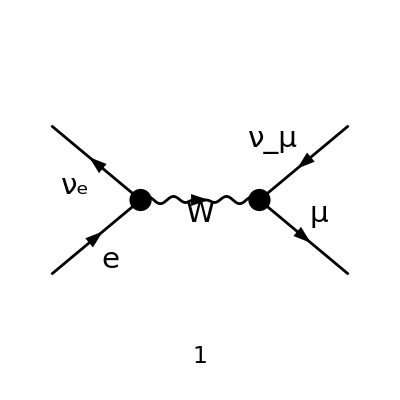

```mathematica
diags=InsertFields[CreateTopologies[0,2->2],{-F[1,{1}],F[2,{1}]}->{-F[1,{2}],F[2,{2}]},InsertionLevel->{Classes},Model->{SM,UnitarySM},GenericModel->{Lorentz,UnitaryLorentz}];
Paint[diags,ColumnsXRows->{2,1},Numbering->Simple,SheetHeader->None,ImageSize->{512,256}];
```

```mathematica
InsertFields[CreateTopologies[0,2->2],{-F[1,{1}],F[2,{1}]}->{-F[1,{2}],F[2,{2}]},InsertionLevel->{Classes},Model->{SM,UnitarySM},GenericModel->{Lorentz,UnitaryLorentz}]
```

TopologyList(Process→{-F(1,{1}),F(2,{1})}→{-F(1,{2}),F(2,{2})},Model→{SM,UnitarySM},GenericModel→{Lorentz,UnitaryLorentz},InsertionLevel→{Classes},ExcludeParticles→{},ExcludeFieldPoints→{},LastSelections→{})(Topology(1)(Propagator(Incoming)(Vertex(1)(1),Vertex(3)(5),Field(1)),Propagator(Incoming)(Vertex(1)(2),Vertex(3)(5),Field(2)),Propagator(Outgoing)(Vertex(1)(3),Vertex(3)(6),Field(3)),Propagator(Outgoing)(Vertex(1)(4),Vertex(3)(6),Field(4)),Propagator(Internal)(Vertex(3)(5),Vertex(3)(6),Field(5)))→Insertions(Generic)(FeynmanGraph(1,Generic==1)(Field(1)→-F(1,{1}),Field(2)→F(2,{1}),Field(3)→F(1,{2}),Field(4)→-F(2,{2}),Field(5)→V)→Insertions(Classes)(FeynmanGraph(1,Classes==1)(Field(1)→-F(1,{1}),Field(2)→F(2,{1}),Field(3)→F(1,{2}),Field(4)→-F(2,{2}),Field(5)→V(3)))))

```mathematica
InsertFields[CreateTopologies[0,2->2],{-F[1,{1}],F[2,{1}]}->{-F[1,{2}],F[2,{2}]},InsertionLevel->{Classes},Model->{SM,UnitarySM},GenericModel->{Lorentz,UnitaryLorentz}]
```

InsertFields(CreateTopologies(0,2→2),{-F(1,{1}),F(2,{1})}→{-F(1,{2}),F(2,{2})},InsertionLevel→{Classes},Model→{SM,UnitarySM},GenericModel→{Lorentz,UnitaryLorentz})

```mathematica
FileNameJoin[{$UserBaseDirectory,"Applications","FeynCalc","Examples"}]
```

/home/timeflux/.Mathematica/Applications/FeynCalc/Examples

```mathematica
SystemOpen["/home/timeflux/.Mathematica/Applications/FeynCalc/Examples"]
```

```mathematica
description="Anel El -> Anmu Mu, EW, total cross section, tree";
If[$FrontEnd===Null,$FeynCalcStartupMessages=False;
Print[description];];
If[$Notebooks===False,$FeynCalcStartupMessages=False];
$LoadAddOns={"FeynArts"};
Get["FeynCalc`"]
$FAVerbose=0;
FCCheckVersion[9,3,0];
```

FeynCalc 9.3.1 (stable version). For help, use the documentation center, check out the wiki or visit the forum.

To save your and our time, please check our FAQ for answers to some common FeynCalc questions.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 256 (2020) 107478, arXiv:2001.04407.

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 207 (2016) 432-444, arXiv:1601.01167.

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun. 64 (1991) 345-359.

FeynArts 3.11 (25 Mar 2022) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

```mathematica
MakeBoxes[q1,TraditionalForm]:="\!\(\*SubscriptBox[\(q\), \(1\)]\)";
MakeBoxes[q2,TraditionalForm]:="\!\(\*SubscriptBox[\(q\), \(2\)]\)";
MakeBoxes[pe,TraditionalForm]:="\!\(\*SubscriptBox[\(p\), \(e\)]\)";
MakeBoxes[pm,TraditionalForm]:="\!\(\*SubscriptBox[\(p\), \(m\)]\)";
InitializeModel[{SM,UnitarySM},GenericModel->{Lorentz,UnitaryLorentz}];
```

```mathematica
diags=InsertFields[CreateTopologies[0,2->2],{-F[1,{1}],F[2,{1}]}->{-F[1,{2}],F[2,{2}]},InsertionLevel->{Classes},Model->{SM,UnitarySM},GenericModel->{Lorentz,UnitaryLorentz}];
Paint[diags,ColumnsXRows->{2,1},Numbering->Simple,SheetHeader->None,ImageSize->{512,256}];
```